## Alec Ramos / Alexander Perry HW 2

### 1. Mathematical problems

```mathematica
1
```

```mathematica
f[x_]:= x^5-302 x^3+893 x^2+1208x-3588
```

```mathematica
FindRoot[f[x], {x, 3}]
```

{x→1.07858}

```mathematica
FindRoot[f[x], {x, -2}]
```

{x→-2.0081}

```mathematica
FindRoot[f[x], {x, 2}]
```

{x→1.98717}

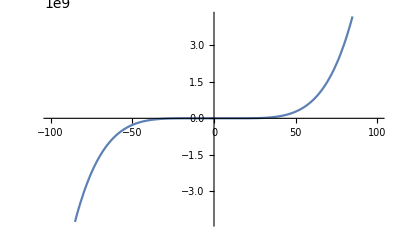

```mathematica
Plot[f[x], {x, -100, 100}]
```

Shows the end behavior of the function.

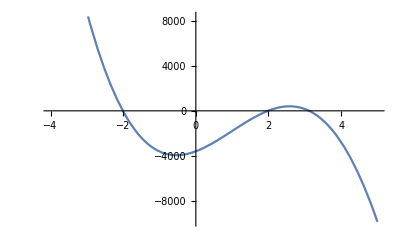

```mathematica
Plot[f[x], {x, -4,5}]
```

Shows the 3 zeros, y intercept, and relative minimum and maximum.

```mathematica
2
```

```mathematica
f[x]=(-3 x^3-3x+7)/(3 x^2-59x-20);
```

```mathematica
FindMinimum[f[x], {x, -2}]
```

{0.282986,{x→-1.33154}}

```mathematica
NSolve[f[x]==0, x]
```

{{x→-0.53929-1.36839 ⅈ},{x→-0.53929+1.36839 ⅈ},{x→1.07858}}

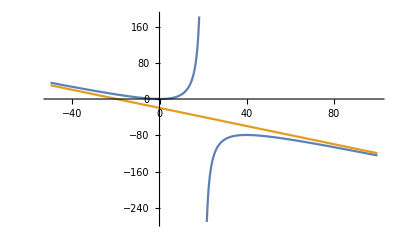

```mathematica
Plot[{f[x], -x-59/3}, {x, -50, 100}]
```

This graph shows the slant asymptote at y = -x-59/3, the vertical asymptote at x = 20, relative minimum, relative maximum, and the end behavior.

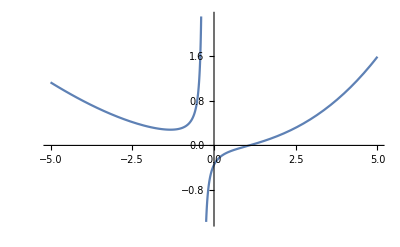

```mathematica
Plot[f[x], {x, -5, 5}]
```

This graph shows the vertical asymptote at x = -1/3, the y intercept, relative minimum, and the zero of the function.

```mathematica
Limit[f[x], x->∞]
```

-∞

```mathematica
Limit[f[x], x->-∞]
```

∞

```mathematica
3
```

```mathematica
f[x]:=(-3 x^3-3x+7+10*2^(.001x))/(3 x^4-27 x^3-2^(.001x))
```

```mathematica
FindRoot[f[x], {x, 40000}]
FindRoot[f[x], {x, 0}]
```

{x→44597.}

{x→1.59704}

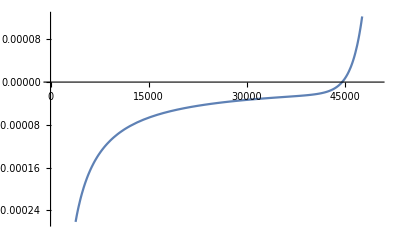

```mathematica
Plot[f[x], {x, 0, 50000}]
```

Shows one zero of the function

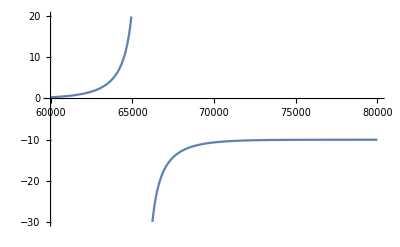

```mathematica
Plot[f[x], {x, 60000, 80000}]
```

```mathematica
Limit[f[x], x->∞]
```

-10.

Shows vertical asymptote and end behavior as the function approaches ∞.

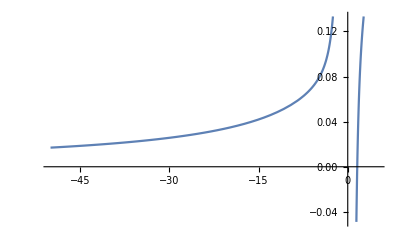

```mathematica
Plot[f[x], {x, -50, 5}]
```

Shows the zero of the function and the end behavior as the function approaches -∞.

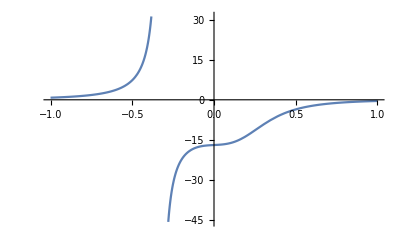

```mathematica
Plot[f[x], {x, -1, 1}]
```

Shows y intercept and vertical asymptote.

#### 4

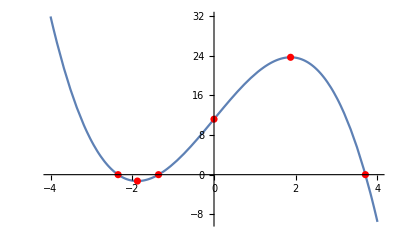

```mathematica
Show[Plot[Log[5x+500]+x^3/20-x^3+10x+5,{x,-4,4}],ListPlot[{{-1.87413,-1.29212},{1.87409,23.721},{-2.34653,0},{-1.3580,0},{3.7045,0},{0,5+Log[500]}},PlotStyle->Red]]
```

Shows zeros of the function, relative minimum,  maximum, and y intercept.

```mathematica
FindMinimum[Log[5x+500]+x^3/20-x^3+10x+5,{x,-3,4}]
```

{-1.29212,{0→-1.87413}}

```mathematica
FindMaximum[Log[5x+500]+x^3/20-x^3+10x+5,{x,0,4}]
```

{23.721,{0→1.87409}}

```mathematica
FindMaximum[Log[5x+500]+x^3/20-x^3+10x+5,{x,0,4}]
```

{23.721,{0→1.87409}}

```mathematica
(* list of roots *)
```

```mathematica
FindRoot[Log[5x+500]+x^3/20-x^3+10x+5,{x,4}]
FindRoot[Log[5x+500]+x^3/20-x^3+10x+5,{x,-4}]
FindRoot[Log[5x+500]+x^3/20-x^3+10x+5,{x,-1}]
```

{0→3.70449}

{0→-2.34653}

{0→-1.35802}

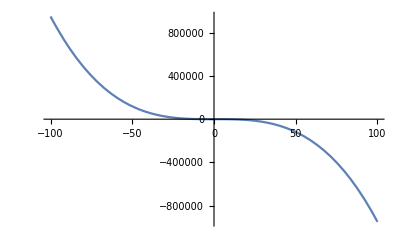

```mathematica
Plot[Log[5x+500]+x^3/20-x^3+10x+5,{x,-100,100}]
```

The graph shows the end behavior of the function.

#### 5

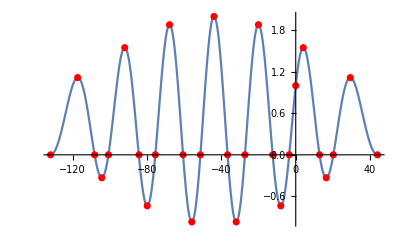

```mathematica
Show[Plot[(Cos[x/7])^2+Sin[x/4],{x,-42Pi,14Pi}],ListPlot[{{-100.801,0},{-12.4061,0},{-3.5093,0},{-108.2140,0},{-131.947,0},{-51.2886,0},{-60.6329,0},{-75.5585,0},{-84.335,0},{-36.676,0},{-27.3317,0},{12.8371,0},{20.2496,0},{43.9823,0},{0,1},{-117.324,1.11605},{-92.038,1.5491},{-67.90006,1.88036},{-43.9823,2},{-20.064,1.88036},{4.07345,1.54916},{29.3596,1.11605},{16.4172,-0.331621},{-8.04593,-.737163},{-32.0333,-0.969676},{-55.9313,-0.969676},{-79.9187,-0.737163},{-104.382,-0.331621}},PlotStyle->Red]]
```

```mathematica
FunctionPeriod[(Cos[x/7])^2+Sin[x/4],{x}]
FindRoot[(Cos[x/7])^2+Sin[x/4],{x,30}];
(Cos[x/7])^2+Sin[x/4];
FindMaximum[(Cos[x/7])^2+Sin[x/4],{x,6π,14π}];
FindMinimum[(Cos[x/7])^2+Sin[x/4],{x,-36π,14π}];
```

{56 π}

The Graph is nice because I used the FunctionPeriod to give me the period of 56Pi, I found all the local min and max using the FindMaximum and FindMInimum Function. The end behavior repeats the graph over a period of 56Pi.

## ii.Sum of Primes

```mathematica
(*This method goes through each prime sum addition and returns the longest string of prime sums that are lower than the upper bound.*)
primeSum[strt_,upperbound_]:= Module[{sum=0,cnt = strt,ansList={},ans={{0,0}},cnt2=1},
While[sum <upperbound,            (*This loop adds all the primes from a starting value and checks to see if the sums are primes and if they are puts them in a list*)
sum+= Prime[cnt];
If[sum>upperbound,Break[]];        (*Kills the loop after it exceeds the upperbound*)
If[PrimeQ[sum], 
AppendTo[ansList,{cnt-strt+1,sum}];
];
cnt++;
];
While[cnt2 ≤ Length[ansList],    (*This loop checks the list of sums and determines which is the longest*)
If[ans[[1,1]]< ansList[[cnt2,1]],
ans[[1]]= ansList[[cnt2]]];
cnt2++;
];
Return[ans]
]
```

```mathematica
(*This method runs through each starting prime running the primeSum of each starting value and adding it to a lst and returning the largest Prime Sum*)
longestPrimeSum[upperbound_]:= Module[{cnt= 1, ans={{0,0,0}}, ansList={},cnt2=1, Primes={}},
While[cnt≤ upperbound,          (*this loop changes the starting values of primeSum and records the answers it gets back into a list*)
Primes = primeSum[cnt,upperbound];
If[Primes[[1,2]]==0,          (*Breaks the loop after the primes get too large to fit in the upper bound*)
Break[]];
AppendTo[ansList,{cnt,Primes[[1,1]],Primes[[1,2]]}];
cnt++;
];
While[cnt2 ≤ Length[ansList],          (*Goes through the list and determines which one is the longest returning the starting position the amount added together and the sum*)
If[ans[[1,2]]< ansList[[cnt2,2]],
ans[[1]]= ansList[[cnt2]]];
cnt2++;
];
Return[ans[[1]]]
]
```

```mathematica
longestPrimeSum[160]
longestPrimeSum[5000]
longestPrimeSum[50000]
```

{2,9,127}

{4,45,4651}

{2,137,49279}

### III. The arclength of a function

```mathematica
a
```

```mathematica
(* creates points at regular x intervals, approximating the function that the points are plotted on as the said interval decreases*)findPoints[func_, interval_, pieces_]:=Module[
{cnt = 0, 
(*distance is the interval between each x value*)
distance = (interval[[2]]-interval[[1]])/(pieces),
list ={}},
While[cnt<=pieces,
(*add points that lie on the function to a list*)
AppendTo[list,{interval[[1]]+distance*cnt, func[interval[[1]]+distance*cnt]}];
cnt++
];
list
]
```

```mathematica
f[x_]:=x^3;
```

```mathematica
findPoints[f, {-1, 1}, 5]
```

{{-1,-1},{-3/5,-27/125},{-1/5,-1/125},{1/5,1/125},{3/5,27/125},{1,1}}

```mathematica
g[x_]:=Sin[x^2];
```

```mathematica
findPoints[g, {-4, 4}, 7]
```

{{-4,Sin[16]},{-20/7,Sin[400/49]},{-12/7,Sin[144/49]},{-4/7,Sin[16/49]},{4/7,Sin[16/49]},{12/7,Sin[144/49]},{20/7,Sin[400/49]},{4,Sin[16]}}

```mathematica
b
```

```mathematica
(*plots the function compared to the list generated by findPoints*)
showLinesegments[func_, interval_, pieces_]:=Module[
{set},
set=findPoints[func, interval, pieces];
Show[
Plot[func[x],{x, interval[[1]], interval[[2]]}, PlotStyle->Blue],
(*plot points in black*)
ListPlot[set, PlotStyle->Black],
(*plot line segments connecting points in findPoints*)
ListLinePlot[set, PlotStyle->Red]
]
]
```

```mathematica
h[x_]:=Cos[4x]^2
```

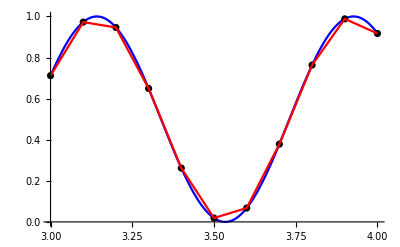

```mathematica
showLinesegments[h, {3,4}, 10]
```

```mathematica
f[x_]:=x^2
```

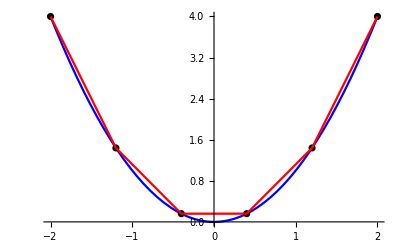

```mathematica
showLinesegments[f, {-2,2}, 5]
```

```mathematica
c
```

```mathematica
(*returns sum of length of line segments between points from findPoints*)
lengthOfCurve[func_, interval_, pieces_]:=Module[
{list, sum=0, cnt=1},
list=findPoints[func, interval, pieces];
While[cnt<Length[list],
(*adding sum from each distance to total sum*)
sum=sum+N@EuclideanDistance[{list[[cnt]]}, {list[[cnt+1]]}];
cnt++
];
sum
]
```

```mathematica
z[x_]:= Sin[x]+Cos[x]+x^3
```

```mathematica
lengthOfCurve[z, {0, 4}, 10]
```

62.0694

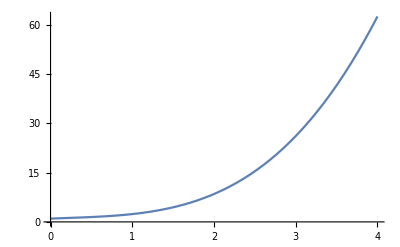

```mathematica
Plot[z[x], {x, 0,4}]
```

```mathematica
q[x_]:=1/2 x^5
```

```mathematica
lengthOfCurve[q, {7.5, 8}, 7]
```

4518.77

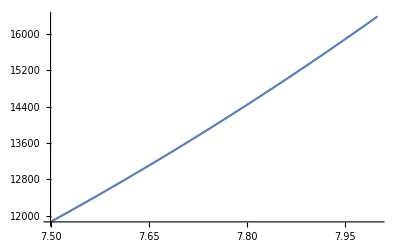

```mathematica
Plot[q[x], {x, 7.5, 8}]
```

```mathematica
d
```

```mathematica
(*finding the length of the arc to some degree of precision*)
preciselengthOfCurve[func_, interval_, precision_]:=Module[
{k=1},
While[
(*iterating lengthOfCurve until doubling the pieces changes the result by less than 10^-precision*)
Abs[lengthOfCurve[func, interval, 2^k]-lengthOfCurve[func, interval, 2^(k+1)]]<10^-precision,
k++;
];
Return[lengthOfCurve[func, interval, 2^(k+1)]]
]
```

```mathematica
y[x_]:=x^2
```

```mathematica
preciselengthOfCurve[y, {0, 8}, 5]
```

64.8087

```mathematica
u[x_]:=7Sec[x]-78965 x^21
```

```mathematica
preciselengthOfCurve[u, {-20, 1}, 3]
```

1.65602×10^32

### IV. Investigate the arclength of families of functions

```mathematica
i
```

```mathematica
f[x_]:=a Sin[x]
```

{{1,3.79009},{2,5.19492},{3,6.88115},{4,8.69184},{5,10.567},{6,12.4792},{7,14.4144},{8,16.3648},{9,18.3256},{10,20.2939},{11,22.2678},{12,24.2459},{13,26.2273},{14,28.2113},{15,30.1974}}

2.16844+1.45943 x+0.0519359 x^2-0.00166011 x^3

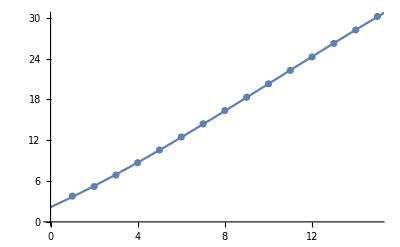

```mathematica
list=Table[{a,preciselengthOfCurve[f, {0,π},6]}, {a,1, 15}]
model=Fit[list,{1, x, x^2, x^3}, x]
Show[ListPlot[list], Plot[model, {x, 0, 16}]]
```

```mathematica
ii
```

{{1,3.81897},{2,8.78457},{3,18.2911},{4,31.1718},{5,50.1189},{6,69.7602},{7,93.329},{8,121.787},{9,149.056},{10,200.025},{11,213.261},{12,239.673},{13,282.582},{14,318.984},{15,362.148}}

1.70046-1.29715 x+2.46752 x^2-0.0532491 x^3

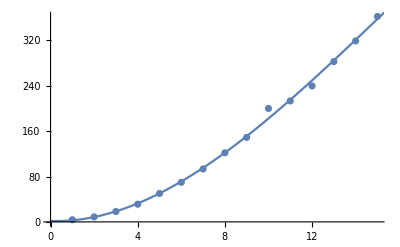

```mathematica
num=1;
list={};
While[num<16,
f[x_]:=num Sin[num x];
update=N@lengthOfCurve[f, {0,π}, 20];
AppendTo[list, {num, update}];
num++;
]
list
model=Fit[list, {1, x, x^2, x^3},x]
Show[ListPlot[list], Plot[model, {x, 0, 16}]]
```

```mathematica
iii
```

```mathematica
bound=1;
num=1;
list={};
While[num<16,
f[x_]:=2*√(-2 x^2+ 2 num^2);
update=N@lengthOfCurve[f, {-num, num}, 15];
AppendTo[list, {num, update}];
num++;
]
list
model=Fit[list, {1, x, x^2, x^3},x]
Show[ListPlot[list], Plot[model, {x, 0, 15}]]
```

```mathematica
iv
```

{{1,3.12721},{2,7.61607},{3,13.0731},{4,19.3343},{5,26.3002},{6,33.9015},{7,42.0866},{8,50.8146},{9,60.0525},{10,69.7726},{11,79.9514},{12,90.5685},{13,101.606},{14,113.048},{15,124.881}}

-0.95255+3.52154 x+0.416926 x^2-0.00619107 x^3

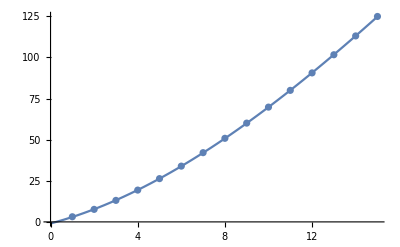

```mathematica
num=1;
list={};
While[num<16,
f[x_]:=√(num^3-num x^2);
update=N@lengthOfCurve[f, {-num, num},15];
AppendTo[list, {num, update}];
num++
]
list
model =Fit[list, {1, x, x^2, x^3}, x]
Show[ListPlot[list], Plot[model, {x, 0, 15}]]
```

```mathematica
v
```

{{1,3.12721},{2,11.0116+0. ⅈ},{3,24.0885+0. ⅈ},{4,36.7521+0. ⅈ},{5,59.864+0. ⅈ},{6,78.2368+0. ⅈ},{7,103.537+0. ⅈ},{8,133.073+0. ⅈ},{9,166.67+0. ⅈ},{10,204.274+0. ⅈ},{11,245.861+0. ⅈ},{12,291.421+0. ⅈ},{13,340.947+0. ⅈ},{14,394.435+0. ⅈ},{15,451.883+0. ⅈ}}

-1.96375+3.6108 x+1.54827 x^2+0.015381 x^3

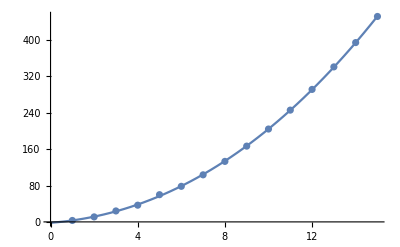

```mathematica
num=1;
list={};
While[num<16,
f[x_]:=√(-num^2 x^2+num^2);
update=N@lengthOfCurve[f, {-num, num}, 15];
AppendTo[list, {num, update}];
num++;
]
list
model=Fit[list, {1, x, x^2, x^3}, x]
Show[ListPlot[list], Plot[model, {x, 0, 15}]]
```